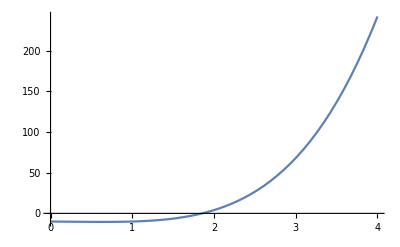

```mathematica
NewtonRaphsonErroriter[x0_,n_,error_,f_]:=Module[{xk1,xk=N[x0]},k=0;
Output={{k,x0,f[x0],None}};
approxError=10000000;
While[n>k&&approxError>error,fPrimexk=f'[xk];
If[fPrimexk==0,
Print["The derivative of function at ",k,"ith iteration is zero, we can not proceed further with the iterative scheme"];Break[]];
xk1=xk-f[xk]/fPrimexk;
approxError=Abs[xk1-xk];
xk=xk1;
k++;
Output=Append[Output,{k,xk,f[xk],approxError}];];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"k","x_k","f[x_k]","ApproxError"}}],8]]
If[k<n,Print["The stated  accuracy  achieved in fewer iterations (less than",n,")"],
Print["Maximum  allowed ",n," iterations are performed, stated accuracy is not achieved"]];
Print["Root after ", k ,"  iterations  x_k=",NumberForm[xk,8]];
Print["Function value at approximated root , f[x_k]=",NumberForm[f[xk],8]];];
f[x_]:=x^4-x-10;
error=10^(-4);
Plot[f[x],{x,0,4}]
```

```mathematica
NewtonRaphsonErroriter[2,5,error,f]
```

k | x_k | f[x_k] | ApproxError
0 | 2 | 4 | None
1 | 1.8709677 | 0.38267457 | 0.12903226
2 | 1.8557807 | 0.0048181285 | 0.01518704
3 | 1.8555846 | 7.9489422×10^-7 | 0.00019614069
4 | 1.8555845 | 1.9539925×10^-14 | 3.2369946×10^-8

The stated  accuracy  achieved in fewer iterations (less than5)

Root after 4  iterations  x_k=1.8555845

Function value at approximated root , f[x_k]=1.9539925×10^-14

```mathematica
NewtonRaphsonErroriter[1,7,error,f]
```

k | x_k | f[x_k] | ApproxError
0 | 1 | -7 | None
1 | 4.2685954 | -9.1443575 | 3.2685954
2 | 5.7646573 | -12.676557 | 1.4960618
3 | 8.4311492 | -9.8802893 | 2.6664919
4 | 8.5781664 | -18.568188 | 0.14701717
5 | 8.9341748 | -15.14397 | 0.35600842
6 | 15.576656 | -25.648537 | 6.6424808
7 | 16.049615 | -21.89247 | 0.47295955

Maximum  allowed 7 iterations are performed, stated accuracy is not achieved

Root after 7  iterations  x_k=16.049615

Function value at approximated root , f[x_k]=-21.89247

Question 2:

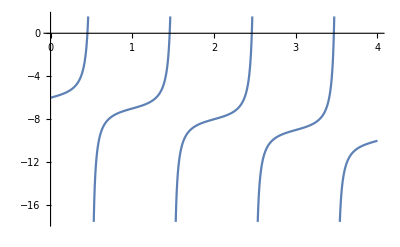

```mathematica
NewtonRaphsonErroriter[x0_,n_,error_,f_]:=Module[{xk1,xk=N[x0]},k=0;
Output={{k,x0,f[x0],None}};
approxError=10000000;
While[n>k&&approxError>error,fPrimexk=f'[xk];
If[fPrimexk==0,
Print["The derivative of function at ",k,"ith iteration is zero, we can not proceed further with the iterative scheme"];Break[]];
xk1=xk-f[xk]/fPrimexk;
approxError=Abs[xk1-xk];
xk=xk1;
k++;
Output=Append[Output,{k,xk,f[xk],approxError}];];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"k","x_k","f[x_k]","ApproxError"}}],8]]
If[k<n,Print["The stated  accuracy  achieved in fewer iterations (less than ",n,")"],
Print["Maximum  allowed ",n," iterations are performed, stated accuracy is not achieved"]];
Print["Root after ", k ,"  iterations  x_k=",NumberForm[xk,8]];
Print["Function value at approximated root , f[x_k]=",NumberForm[f[xk],8]];];
f[x_]:=Tan[Pi*x]-x-6;
error=10^(-5);
Plot[f[x],{x,0,4}]
```

```mathematica
NewtonRaphsonErroriter[0.45,20,error,f]
```

k | x_k | f[x_k] | ApproxError
0 | 0.45 | -0.13624849 | None
1 | 0.45106965 | 0.0029771478 | 0.001069653
2 | 0.45104727 | 1.3607342×10^-6 | 0.000022383938
3 | 0.45104726 | 2.8510527×10^-13 | 1.0240154×10^-8

The stated  accuracy  achieved in fewer iterations (less than 20)

Root after 3  iterations  x_k=0.45104726

Function value at approximated root , f[x_k]=2.8510527×10^-13

```mathematica
NewtonRaphsonErroriter[0.52,20,error,f];
```

k | xk | f[xk] | ApproxError
0 | 0.52 | -22.414545 | None
1 | 0.54816525 | -13.106354 | 0.028165248
2 | 0.64365016 | -8.7070057 | 0.095484917
3 | 1.2047871 | -6.4550114 | 0.5611369
4 | 2.8566646 | -9.3400915 | 1.6518775
5 | 6.104502 | -11.763872 | 3.2478374
6 | 10.798585 | -17.531943 | 4.6940825
7 | 15.374695 | -18.967001 | 4.5761109
8 | 16.30658 | -20.868605 | 0.93188455
9 | 18.722573 | -25.911666 | 2.4159925
10 | 22.658345 | -30.499949 | 3.9357729
11 | 25.041839 | -30.909635 | 2.3834937
12 | 39.114056 | -44.739572 | 14.072217
13 | 56.440441 | -57.15851 | 17.326385
14 | 57.077033 | -62.830188 | 0.63659239
15 | 84.007891 | -89.983095 | 26.930858
16 | 125.98693 | -132.02801 | 41.979041
17 | 187.48416 | -173.40522 | 61.497228
18 | 187.62084 | -196.12726 | 0.13667754
19 | 196.58562 | -206.21309 | 8.9647854
20 | 201.3283 | -205.65784 | 4.7426748

Maximum allowed 20iterations are performed, stated accuracy is not achieved

Root after 20iterations xk= 201.3283

Function value at approximated root, f[xk]= -205.65784

Question 3:

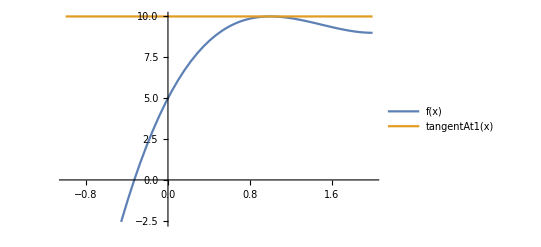

The derivative of function at 0ith iteration is zero, we can not proceed further with the iterative scheme

k | x_k | f[x_k] | ApproxError
0 | 1 | 10 | None

The stated  accuracy  achieved in fewer iterations (less than20)

Root after 0  iterations  x_k=1.

Function value at approximated root , f[x_k]=10.

```mathematica
NewtonRaphsonErroriter[x0_,n_,error_,f_]:=Module[{xk1,xk=N[x0]},k=0;
Output={{k,x0,f[x0],None}};
approxError=10000000;
While[n>k&&approxError>error,fPrimexk=f'[xk];
If[fPrimexk==0,
Print["The derivative of function at ",k,"ith iteration is zero, we can not proceed further with the iterative scheme"];Break[]];
xk1=xk-f[xk]/fPrimexk;
approxError=Abs[xk1-xk];
xk=xk1;
k++;
Output=Append[Output,{k,xk,f[xk],approxError}];];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"k","x_k","f[x_k]","ApproxError"}}],8]]
If[k<n,Print["The stated  accuracy  achieved in fewer iterations (less than",n,")"],
Print["Maximum  allowed",n,"iterations are performed, stated accuracy is not achieved"]];
Print["Root after ", k ,"  iterations  x_k=",NumberForm[xk,8]];
Print["Function value at approximated root , f[x_k]=",NumberForm[f[xk],8]];];
f[x_]:=2*x^3-9*x^2+12*x+5;
tangentAt1[x_]=f[1]+f'[1]*(x-1);
Plot[{f[x],tangentAt1[x]},{x,-1,2},PlotLegends->"Expressions"]
NewtonRaphsonErroriter[1,20,error,f]
```